# CreateRandomFile

Create a file filled with random bytes for testing

## Definition

```mathematica
Get @ FileNameJoin @ { NotebookDirectory[ ], "Definition.wl" };
```

```mathematica
TestReport @ FileNameJoin @ { NotebookDirectory[ ], "Tests.wlt" }
```

## Documentation

### Usage

CreateRandomFile[n]

creates a random file of n bytes in the default area for temporary files on your computer system.

CreateRandomFile["file",n]

creates a random file with name file.

### Details & Options

If "file" has no pathname separators, CreateRandomFile creates a file in your current working directory.

A relative path is interpreted with respect to the current working directory.

CreateRandomFile only creates the file; it does not open it.

The file created can subsequently be opened for reading or writing in binary mode.

CreateRandomFile returns the full name of the file it creates, and $Failed if it cannot create the file.

CreateRandomFile[n] creates a file in the directory specified by the current value of $TemporaryDirectory.

CreateRandomFile[n] is equivalent to CreateRandomFile[Automatic,n].

The default setting CreateIntermediateDirectories→True specifies that intermediate directories should be created as needed.

File["path"] may be used to specify a file name.

## Examples

```mathematica
Quit
```

```mathematica
Options[ResourceFunction[ "MessageFailure" ]]
```

{MessageFunction→Automatic,Verbose→False,Stack→False,TestMode→False}

```mathematica
ResourceFunction["MessageFailure"][Power::infy,HoldForm[1/0],"MessageFunction"->ResourceFunction["ResourceFunctionMessage"]]
```

```mathematica
DefineResourceFunction[CreateRandomFile]
```

[◼] | CreateRandomFile

```mathematica
CreateRandomFile[]
```

CreateRandomFile::argt: CreateRandomFile called with 0 arguments; 1 or 2 arguments are expected.

Failure[…]

```mathematica
ResourceFunction["CreateRandomFile"][ ]
```

ResourceFunction::usermessage: CreateRandomFile

Failure[…]

```mathematica
$failed
```

True

```mathematica
CreateFile[]
```

C:\Users\rhennigan\AppData\Local\Temp\m-49e2cc46-2052-483f-9e0d-ae908fde026b

```mathematica
DeleteObject@CloudObject["temp"]
```

```mathematica
obj=CreateRandomFile[CloudObject[],100]
```

CloudObject[https://www.wolframcloud.com/obj/f34c18af-7eeb-42f3-a505-ffa0c52a6363]

```mathematica
FileSize[obj]
```

100. B

```mathematica
lo=LocalObject["temp"]
```

LocalObject[file:///C:/Users/rhennigan/AppData/Roaming/Wolfram/Objects/temp]

```mathematica
Quiet@DeleteObject@lo
```

$Failed

```mathematica
CreateRandomFile[lo,50]
```

File[C:\Users\rhennigan\AppData\Roaming\Wolfram\Objects\temp\export]

```mathematica
Names["System`*Progress*"]
```

{ProgressIndicator,ProgressIndicatorBox,ProgressIndicatorBoxOptions,ProgressReporting,SystemModelProgressReporting,TrainingProgressCheckpointing,TrainingProgressFunction,TrainingProgressMeasurements,TrainingProgressReporting,$ProgressReporting}

```mathematica
ProgressReporting
```

```mathematica
StringMatchQ[]
```

StringMatchQ::argt: StringMatchQ called with 0 arguments; 1 or 2 arguments are expected.

StringMatchQ[]

```mathematica
RandomReal[1,-5]
```

RandomReal::array: The array dimensions -5 given in position 2 of RandomReal[1,-5] should be a list of non-negative machine-sized integers giving the dimensions for the result.

RandomReal[1,-5]

```mathematica
CreateFile[sldkfj]
```

CreateFile::badfile: The specified argument, sldkfj, should be a valid string or File.

CreateFile::ioarg: I/O operation is not valid for sldkfj.

$Failed

```mathematica
General::argt
```

`1` called with `2` arguments; `3` or `4` arguments are expected.

```mathematica
CreateRandomFile[]
```

CreateRandomFile::invargs: Invalid argument pattern.

Failure[…]

```mathematica
SystemOpen@ExpandFileName[lo]
```

```mathematica
Export[ lo, { }, "Binary" ]
```

CreateDirectory::ioarg: I/O operation is not valid for C:\Users\rhennigan\AppData\Roaming\Wolfram\Objects\temp|abc.

$Failed

```mathematica
CreateFile["temp","temp"]
```

CreateFile::nonopt: Options expected (instead of temp) beyond position 1 in CreateFile[temp,temp]. An option must be a rule or a list of rules.

CreateFile[temp,temp]

```mathematica
f[a|PatternSequence[],b]:=x
```

```mathematica
f[a,b]
```

x

```mathematica
f[b]
```

x

```mathematica
General::nonopt
```

Options expected (instead of `1`) beyond position `2` in `3`. An option must be a rule or a list of rules.

```mathematica
CreateRandomFile::nonopt
```

```mathematica
FileExistsQ[LocalObject["temp"]]
```

True

```mathematica
lo=LocalObject["temp"]
```

LocalObject[file:///C:/Users/rhennigan/AppData/Roaming/Wolfram/Objects/temp]

```mathematica
LocalObjects`AuxPathName @ lo
```

C:\Users\rhennigan\AppData\Roaming\Wolfram\Objects\temp\export

```mathematica
Names["LocalObjects`*"]
```

{LocalObjects`absolutePathQ,LocalObjects`atomicOutput,LocalObjects`atomicRename,LocalObjects`AuxFileName,LocalObjects`AuxPathName,LocalObjects`BundleDirectoryName,LocalObjects`BundlePathName,LocalObjects`ensureDirectory,LocalObjects`fileURIQ,LocalObjects`findLocalObjects,LocalObjects`GetHandler,LocalObjects`getLocalObject,LocalObjects`LocalCopy,LocalObjects`LocalCriticalSection,LocalObjects`LocalDumpSave,LocalObjects`LocalExport,LocalObjects`LocalFileName,LocalObjects`LocalGet,LocalObjects`LocalImport,LocalObjects`LocalObjectQ,LocalObjects`LocalPut,LocalObjects`LocalPutSerialize,LocalObjects`LocalRename,LocalObjects`LocalSave,LocalObjects`LocalSymbolQ,LocalObjects`LocalTestAndPut,LocalObjects`LocalTestAndSet,LocalObjects`mutateSymbol,LocalObjects`nameDecode,LocalObjects`nameEscape,LocalObjects`objectURIQ,LocalObjects`ObjPathName,LocalObjects`PathName,LocalObjects`PathToURI,LocalObjects`putLocalObject,LocalObjects`resolvePath,LocalObjects`setCacheBase,LocalObjects`setLocalBase,LocalObjects`SymbolObject,LocalObjects`testAndPutLocalObject,LocalObjects`testLocalObject,LocalObjects`URIToPath,LocalObjects`WithLocalBundleDirectory,LocalObjects`$cacheBaseAuto,LocalObjects`$defaultFields,LocalObjects`$defaultHandler,LocalObjects`$inputFields,LocalObjects`$localBaseAuto,LocalObjects`$localCacheBase,LocalObjects`$objectFile,LocalObjects`$sandboxMode,LocalObjects`$tmpDirectory}

### Basic Examples

Create a file containing 50 random bytes:

```mathematica
CreateRandomFile[50]
```

File[C:\Users\rhennigan\AppData\Local\Temp\m-d526c831-208f-4b86-8913-4d09420eb405]

```mathematica
DeleteFile["file.bin"]; $Line=0;
```

Create a random file at a specified path:

```mathematica
CreateRandomFile["file.bin",50]
```

File[H:\Documents\file.bin]

Verify the file size:

```mathematica
FileSize["file.bin"]
```

50. B

View the contents:

```mathematica
ReadString["file.bin"]
```

}|mX.16~.7f.0bZ8ÿ.93.9f:Q0á.023ô.87 §?:.81.81¡~.80.85.10ØB.06ÛÀ
.044.07\fãÊ.154jøÿ.86

Cleanup:

```mathematica
DeleteFile["file.bin"]
```

### Scope

### Options

```mathematica
Options[CreateRandomFile]
```

{CreateIntermediateDirectories→True,BatchSize→Automatic,OpenAppend→False,OverwriteTarget→False,ShowProgress→True}

#### CreateIntermediateDirectories

By default, the parent directory will be created for the file if it does not already exist:

```mathematica
path = FileNameJoin @ { $TemporaryDirectory, CreateUUID[ ], CreateUUID[ ] }
```

C:\Users\rhennigan\AppData\Local\Temp\feafacd5-145c-496d-a7ef-b51bc5d80872\202ea73d-fede-475d-adf3-6afcca21eae1

```mathematica
CreateRandomFile[path,50]
```

File[C:\Users\rhennigan\AppData\Local\Temp\feafacd5-145c-496d-a7ef-b51bc5d80872\202ea73d-fede-475d-adf3-6afcca21eae1]

Do not create a file if the parent directory does not exist:

```mathematica
path = FileNameJoin @ { $TemporaryDirectory, CreateUUID[ ], CreateUUID[ ] }
```

C:\Users\rhennigan\AppData\Local\Temp\43fe277a-ef7b-4f95-ae29-1a801700d525\0c2a9f47-e1b7-4b24-9282-c9017b4da11e

```mathematica
CreateRandomFile[path,50,CreateIntermediateDirectories->False]
```

ResourceFunction::usermessage: CreateRandomFile

CreateRandomFile[C:\Users\rhennigan\AppData\Local\Temp\43fe277a-ef7b-4f95-ae29-1a801700d525\0c2a9f47-e1b7-4b24-9282-c9017b4da11e,50,CreateIntermediateDirectories→False]

#### OverwriteTarget

By default, CreateRandomFile will not overwrite existing files:

```mathematica
Put["hello","file.txt"]
```

```mathematica
CreateRandomFile["file.txt",50]
```

ResourceFunction::usermessage: CreateRandomFile

CreateRandomFile[file.txt,50]

Overwrite the target file if it already exists:

```mathematica
Put["hello","file.txt"]
```

```mathematica
CreateRandomFile["file.txt",50,OverwriteTarget->True]
```

File[H:\Documents\file.txt]

```mathematica
FilePrint["file.txt"]
```

N Ûz'gp.93.0fÔÄ¨ÉQÄ..b9ä_.94ö.16Ë.90ÃÇr$.12isò.a6â.9e?VcKW7aü·.85*Ê.b9>d

### Applications

Create a file for testing performance of different file hashing methods:

```mathematica
file=CreateRandomFile[1000000]
```

File[C:\Users\rhennigan\AppData\Local\Temp\m-54c37e1b-4ede-4fc8-a32c-b3ad23ff2e99]

```mathematica
timings=AssociationMap[
First[RepeatedTiming[FileHash[file,#]]]&,
{"Adler32","CRC32","Keccak224","Keccak256","Keccak384","Keccak512","MD2","MD4","MD5","RIPEMD160","RIPEMD160SHA256","SHA","SHA256","SHA256SHA256","SHA3-224","SHA3-256","SHA3-384","SHA3-512","SHA384","SHA512"}]
```

<|Adler32→0.0141,CRC32→0.0146,Keccak224→0.025,Keccak256→0.025,Keccak384→0.029,Keccak512→0.036,MD2→0.169,MD4→0.015,MD5→0.015,RIPEMD160→0.017,RIPEMD160SHA256→0.016,SHA→0.015,SHA256→0.018,SHA256SHA256→0.017,SHA3-224→0.018,SHA3-256→0.018,SHA3-384→0.019,SHA3-512→0.021,SHA384→0.016,SHA512→0.015|>

```mathematica
BarChart[ReverseSort[timings],ChartLabels->Automatic,ScalingFunctions->"Log",BarOrigin->Left]
```

-Graphics-

Create a cloud object with random data for testing download speeds:

```mathematica
file=CreateRandomFile[25000000];
obj=CopyFile[file,CloudObject[Permissions->"Public"]]
```

CloudObject[https://www.wolframcloud.com/obj/22eb3268-6ef1-48d9-9e93-90f48d14d01b]

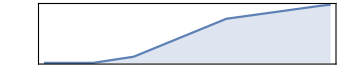
Download Progress
Source | CloudObject[https://www.wolframcloud.com/obj/22eb3268-6ef1-48d9-9e93-90f48d14d01b]
Destination | File[H:\Documents\f32655d4-c598-4d5c-8fa1-465209ce2398]
Progress | 
Downloaded | 25.0 MB / 25.0 MB
Elapsed Time | 2.2 s
Remaining Time | 0 ns
 | -Graphics-
 | Abort

<|Destination→File[H:\Documents\f32655d4-c598-4d5c-8fa1-465209ce2398],TaskObject→TaskObject[<|TaskUUID -> 27286c51-7036-4054-9bd1-82cda871f888, TaskEnvironment -> External, TaskType -> Asynchronous, AsynchronounsTaskID -> 8, EvaluationExpression :> None, HandlerFunctions -> <||>, HandlerFunctionsKeys -> {ByteCountDownloaded, ByteCountTotal}, AutoRemove -> True|>],CellObject→58895889Print|>

```mathematica
ResourceFunction["MonitoredDownload"][obj]
```

```mathematica
DeleteFile/@{file,obj}
```

{Null,Null}

### Properties and Relations

CreateRandomFile writes data in batches, so memory usage won't exceed what's available:

```mathematica
MemoryAvailable[]
```

37842173952

```mathematica
MaxMemoryUsed[file=CreateRandomFile[50000000000]]
```

3515787504

```mathematica
DeleteFile[file]
```

### Possible Issues

### Neat Examples

## Source & Additional Information

### Contributed By

Richard Hennigan (Wolfram Research)

### Keywords

keyword 1

### Categories

Cloud & Deployment |  Core Language & Structure
 Data Manipulation & Analysis |  Engineering Data & Computation
 External Interfaces & Connections |  Financial Data & Computation
 Geographic Data & Computation |  Geometry
 Graphs & Networks |  Higher Mathematical Computation
 Images |  Just For Fun
 Knowledge Representation & Natural Language |  Machine Learning
 Notebook Documents & Presentation |  Programming Utilities
 Repository Tools |  Scientific and Medical Data & Computation
 Social, Cultural & Linguistic Data |  Sound & Video
 Strings & Text |  Symbolic & Numeric Computation
 System Operation & Setup |  Time-Related Computation
 User Interface Construction |  Visualization & Graphics

### Related Symbols

CreateFile

BinaryWrite

CreateDirectory

DeleteFile

RenameFile

CopyFile

### Related Resource Objects

FileQ

EnsureFilePath

FileDownloadResponse

OpenStreamQ

### Source/Reference Citation

Source, reference or citation information

### Links

Link to other related material

### Tests

```mathematica
MyFunction[x,y]
```

x y

### Compatibility

#### Wolfram Language Version

12.3+

#### Operating System

Windows |  Mac |  Unix

#### Required Features

Notebooks |  Parallel Kernels |  Cloud Access

#### Environments

SessionLocal or cloud interactive session |  ScriptScript run in batch mode |  SubkernelParallel or grid subkernel
 WebEvaluationCloud evaluation initiated by an HTTP request |  WebAPIAPI called through an HTTP request |  ScheduledScheduled task
 BatchJobRemote batch job |  |

#### Cloud Support

Supported in cloud

## Author Notes

Additional information about limitations, issues, etc.

## Submission Notes

Additional information for the reviewer.